```mathematica
{a,b}~Join~{c,d}
```

{a,b,c,d}

```mathematica
List[Sequence[a,b,c],Sequence[c,d]]
```

{a,b,c,c,d}

```mathematica
AstronomicalData["Planet","SemimajorAxis"][[;;,1]]
```

{5.790918×10^10,1.082089×10^11,1.4959789×10^11,2.2793664×10^11,7.7841203×10^11,1.4267254×10^12,2.87097222×10^12,4.49825291×10^12}

```mathematica
objs=List[Sequence@@AstronomicalData["Planet"],
Sequence@@AstronomicalData["DwarfPlanet"],
Sequence@@AstronomicalData["MinorPlanet"]]
moons=Sequence@@AstronomicalData["Moons"]
```

{Mercury,Venus,Earth,Mars,Jupiter,Saturn,52001,Eris,MinorPlanet15874Provisional1996TL66,MinorPlanet26181Provisional1996GQ21,MinorPlanet29981Provisional1999TD10,Sedna,Moons}
 |  |  |  |

```mathematica
AstronomicalData["ObjectType"]
```

PlanetaryMoon

```mathematica
(sascache[#]=AstronomicalData[#,"SemimajorAxis"])&/@(AstronomicalData["Planet"]~Join~AstronomicalData["DwarfPlanet"])
```

{5.790918×10^10 m,1.082089×10^11 m,1.4959789×10^11 m,2.2793664×10^11 m,7.7841203×10^11 m,1.4267254×10^12 m,2.87097222×10^12 m,4.49825291×10^12 m,4.13781191×10^11 m,5.90637627×10^12 m,6.475×10^12 m,6.822×10^12 m,1.013×10^13 m}

```mathematica
sas=AstronomicalData[#,"SemimajorAxis"][[1]]&/@objs
ms=AstronomicalData[#,"Mass"][[1]]&/@objs
```

```mathematica
types={"Planet","DwarfPlanet","MinorPlanet"}
moontypes={"PlanetaryMoon"}
sasnorm=AstronomicalData[#,"SemimajorAxis"][[;;,1]]&/@types;
ms=AstronomicalData[#,"Mass"][[;;,1]]&/@(types~Join~moontypes);
```

{Planet,DwarfPlanet,MinorPlanet}

{PlanetaryMoon}

```mathematica
sasmoon=((sascache/@(AstronomicalData[#,"OrbitCenter"]))[[;;,1]])&/@moontypes;
sas=sasnorm~Join~sasmoon;
```

```mathematica
sas[[1,1]]
```

5.790918×10^10

```mathematica
ms[[1,1]]
```

3.30104×10^23

```mathematica
(a/5.790917567476446063`7.999956572723137*^10)^(9/8)*3.30104`6.*^23/130
```

1.9798×10^9 a^(9/8)

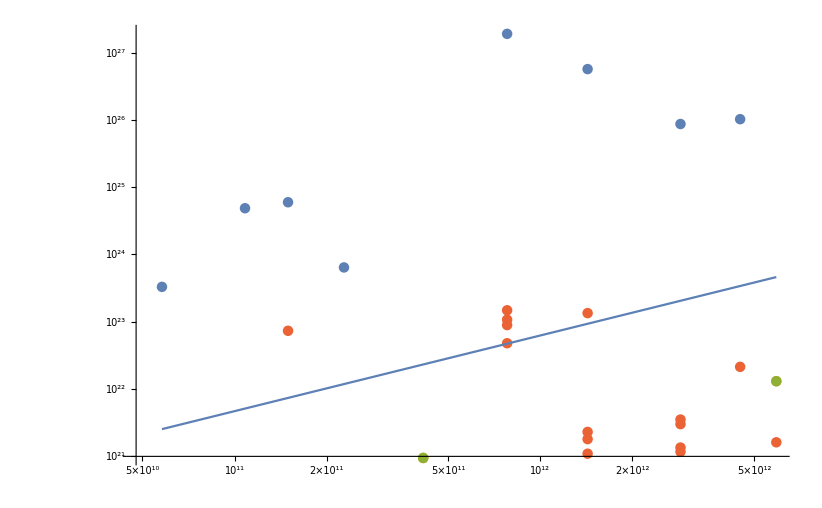

```mathematica
Show[ListLogLogPlot[Transpose/@Transpose[{sas,ms}],PlotRange->{All,{10^21,All}}],
LogLogPlot[1.9798*^9 a^(9/8),{a,sas[[1,1]],sas[[2,2]]}]]
```

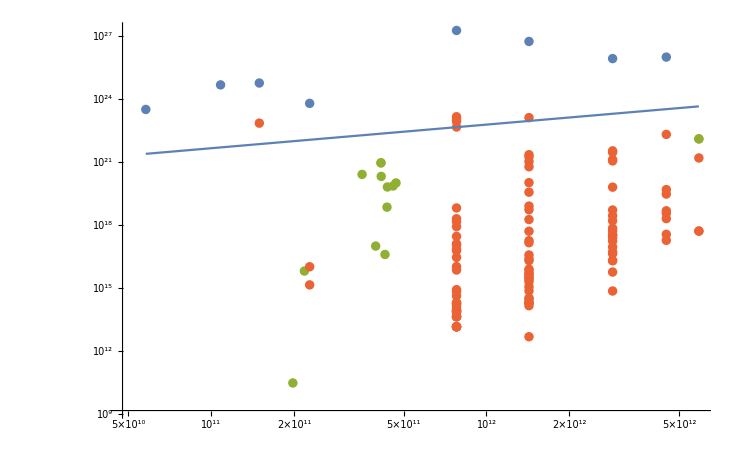

```mathematica
Show[ListLogLogPlot[Transpose/@Transpose[{sas,ms}]],
LogLogPlot[1.9798*^9 a^(9/8),{a,sas[[1,1]],sas[[2,2]]}]]
```

```mathematica
AstronomicalData["Ganymede","OrbitCenter"]
```

Jupiter

```mathematica
(AstronomicalData[#,"SemimajorAxis"][[1]]&/@AstronomicalData["DwarfPlanet"])
```

{4.13781191×10^11,5.90637627×10^12,6.475×10^12,6.822×10^12,1.013×10^13}

```mathematica
AstronomicalData[]
```

{11ComaeBerenicesb,11UrsaeMinorisb,14Andromedaeb,14Herculisb,16CygniBb,18Delphinib,24Sextantisb,24Sextantisc,156755,Zwerling,Zwetana,Zwicky,Zwiers,Zwin,Zwingli,Zykina,Zyskin}
 |  |  |  |

```mathematica
AstronomicalData[#,"SemimajorAxis"]&/@AstronomicalData["DwarfPlanet"]
```

{4.13781191×10^11 m,5.90637627×10^12 m,6.475×10^12 m,6.822×10^12 m,1.013×10^13 m}

```mathematica
%6[[1,1]]//InputForm
```

4.1378119144969666124964654`9.49862880716732*^11